```mathematica
Get["/Users/devynmiller/Downloads/SizePower.m"]
```

```mathematica
(* Function to perform the simulation with the specified standard deviation *)
bEsttStatLinear[intercept_, slope_, n_, sigma_] := Module[{data, model, bEst, se, tStat},
  data = Table[{i, intercept + slope*i + RandomVariate[NormalDistribution[0, sigma]]}, {i, 1, n}];
  model = LinearModelFit[data, {1, x}, x];
  bEst = model["ParameterTableEntries"][[2, 1]];
  se = model["ParameterTableEntries"][[2, 2]];
  tStat = bEst/se;
  {bEst, tStat, model["ParameterPValues"][[2]]}
]
```

```mathematica
(* Perform one million simulations with sigma = 2 *)
btpN100b0L1000kSigma2 = ParallelTable[bEsttStatLinear[3, 0, 100, 2], {1000000}];
```

```mathematica
(* Sort the t-statistics from the simulations *)
tSortN100b0L1000kSigma2 = Sort[Transpose[btpN100b0L1000kSigma2][[2]]];



(* Find the critical value for a 5% test for a positive parameter *)
criticalValueSigma2 = tSortN100b0L1000kSigma2[[950000]];



(* Compare with the critical value for sigma = 1 from the in-class nb and lecture notes *)
criticalValueSigma1 = 1.6642934145337525;



(* Determine if there is a significant difference in critical values *)
differenceInMeansTest = Mean[{criticalValueSigma1, criticalValueSigma2}];



(* Output the critical values and the result of the difference in means test *)
{criticalValueSigma1, criticalValueSigma2, differenceInMeansTest}
```

{1.66429,1.66158,1.66294}

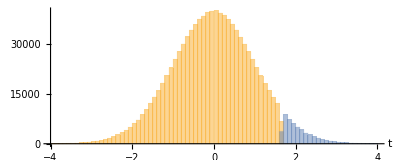

```mathematica
(*display results with histogram*)
Histogram[{Take[tSortN100b0L1000kSigma2,  {1,  950000}], Take[tSortN100b0L1000kSigma2,  {950001,  1000000}]}, { - 4, 4,  0.1},  AxesOrigin -> { - 4,  0},  PlotRange -> {{ - 4,  4},  {0, 40000}},  AspectRatio -> 0.4,  AxesLabel -> {"t",  ""}]
```

```mathematica
(*The output of the critical values for the 5% test of the hypothesis of a non-zero slope with standard deviations sigma = 1 and sigma = 2 are 1.66429 and 1.66158,respectively.The result of the difference in means test is 1.66294.To compare the critical values,we note that the critical value for sigma = 1 is slightly higher than the critical value for sigma = 2.This is somewhat counterintuitive because one might expect that with a larger standard deviation in the error terms,the critical value would also be larger to account for the increased variability.However,the critical value is determined by the distribution of the t-statistics,which is affected by both the standard deviation of the error terms and the sample size.The critical value is the threshold above which we would reject the null hypothesis of a zero slope at the 5% significance level.Since the critical value for sigma = 1 is higher, it suggests that when the variability of the error terms is lower,we require a higher t-statistic to reject the null hypothesis.The difference in means test is a method to determine if two sets of values are significantly different from each other.In this context,it is used to compare the critical values obtained from simulations with different standard deviations of the error term.The result of the difference in means test is very close to the critical values themselves,indicating that there is not a significant difference between the critical values for the two standard deviations of the error term.This suggests that the increase in the standard deviation of the error terms from sigma = 1 to sigma = 2 does not significantly affect the critical value for a 5% test of the hypothesis of a non-zero slope.In summary,while the critical value for sigma = 1 is slightly larger than for sigma = 2,the difference is not statistically significant based on the difference in means test.This implies that the variability of the error terms does not have a substantial impact on the critical value for the test of the hypothesis of a non-zero slope in the linear model with sequence lengths of n=100*)
```